```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2, 0≤x≤1}, {c11(x-1)+c12(x-1)^2, 1<x≤2}, {c21(x-2)+c22(x-2)^2, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c01+c02

c11+c12

c21+c22

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+2]+f[x+1]+f[x]+f[x-1]+f[x-2]+f[x-3],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-2f[x+2]-f[x+1]+f[x-1]+2f[x-2]+3f[x-3],x>0&&x<1],x]
```

{2+c01+c02+c11+c12+c21+c22,-2 (c02+c12+c22),2 (c02+c12+c22)}

{1+c01+c02+2 c11+2 c12+3 c21+3 c22,-c01-2 c02-3 c11-4 c12-5 c21-6 c22,c02+c12+c22}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0
	},
	{c01,c02,c11,c12,c21,c22}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c02→-1-c01,c12→-c11,c21→-1-c01-c11,c22→1+c01+c11}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>3&&y<4]
}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1a6}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]],
	FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1a6,{{x,y}}]]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-3&&y<-2]
}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5,DSumF1b6}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]],
	FullSimplify[D[SumF1b5,{{x,y}}]],
	FullSimplify[D[SumF1b6,{{x,y}}]]
}];
```

```mathematica
DSumF1a1=Simplify[DSumF1a1/.φ->1/2];
DSumF1a2=Simplify[DSumF1a2/.φ->1/2];
DSumF1a3=Simplify[DSumF1a3/.φ->1/2];
DSumF1a4=Simplify[DSumF1a4/.φ->1/2];
DSumF1a5=Simplify[DSumF1a5/.φ->1/2];
DSumF1a6=Simplify[DSumF1a6/.φ->1/2];
DSumF1b1=Simplify[DSumF1b1/.φ->1/2];
DSumF1b2=Simplify[DSumF1b2/.φ->1/2];
DSumF1b3=Simplify[DSumF1b3/.φ->1/2];
DSumF1b4=Simplify[DSumF1b4/.φ->1/2];
DSumF1b5=Simplify[DSumF1b5/.φ->1/2];
DSumF1b6=Simplify[DSumF1b6/.φ->1/2];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1a6}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-2^-1 (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_3^4 ∫_-2^-1 (DSumF1a6.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5,Err1b6}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_3^4 (DSumF1b5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-3^-2 ∫_3^4 (DSumF1b6.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1a6+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5+Err1b6];
```

```mathematica
Err=Err1
DErr=FullSimplify[D[Err,{{c01,c11}}]];
H=FullSimplify[D[Err,{{c01,c11},2}]];
Sols=Solve[DErr==0,{c01,c11}];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/1440(4373+760 c01^4+5 c01^3 (1051+276 c11)+3 c01^2 (4381+6 c11 (405+62 c11))+3 c11 (2146+c11 (1099+4 c11 (53+13 c11)))+c01 (12826+3 c11 (4176+c11 (1299+152 c11))))

1 | 0.0343838 | True
2 | 0.819269+0.493763 ⅈ | False
3 | 0.819269-0.493763 ⅈ | False
4 | 1.06321+0.252926 ⅈ | False
5 | 1.06321-0.252926 ⅈ | False
6 | 1.08507+0.215646 ⅈ | False
7 | 1.08507-0.215646 ⅈ | False
8 | 0.179691+0.00719426 ⅈ | False
9 | 0.179691-0.00719426 ⅈ | False

```mathematica
RootReduce[Sols[[1]]]
```

{c01→Root[107304086230531885+599287446548831718 #1+1400958868626252747 #1^2+1834238645594718312 #1^3+1498904274881813490 #1^4+798582300168995568 #1^5+278783851306490292 #1^6+61715710273939056 #1^7+7883190806676480 #1^8+443705711242240 #1^9&,1],c11→Root[18431582450625+23718361748580 #1+334904447070675 #1^2-37839981285332 #1^3-288829159903530 #1^4-336831488617800 #1^5-632563845450300 #1^6+2304156770184864 #1^7-1637392551713280 #1^8+354964568993792 #1^9&,1]}

{c02→-0.442669,c12→0.596792,c21→0.154123,c22→-0.154123,c01→-0.557331,c11→-0.596792}

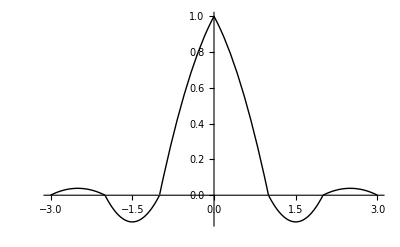

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```